# Data Analysis

Some data are imported from julia code https://github.com/djuliannader/RabiModel

## Figure 1

```mathematica
gt=1.2;
λt=0.0;
H[x_,p_,g_,λ_]=(p^2+x^2)/2-(1/2)*(1+(2^(1/2)*g*x+λ)^2)^(1/2);
FindMinimum[H[x,0,gt,λt],{x,-7,7}]
```

{-0.533611,{x→0.610567}}

### Data

```mathematica
Ec1=-0.5;
Ec2=-0.550625;
Ec3=-0.5700940377221317;
datE0Q1={{10,-5.146947924790874},{20,-10.157004099708788},{30,-15.160796965487021},{40,-20.162795596159025},{50,-25.164030940258368},{60,-30.164870515456588},{70,-35.1654783837978},{80,-40.1659388891384},{90,-45.16629985081335},{100,-50.16659041002165}};
datE0Q2={{10,-5.700728683371035},{20,-11.14844030082671},{30,-16.643654532259983},{40,-22.14702806081865},{50,-27.651891728963918},{60,-33.157274492533745},{70,-38.66292302164267},{80,-44.16873047623011},{90,-49.67464107498637},{100,-55.18062247933808}};
datE0Q3={{10,-5.827407188450129},{20,-11.512498096551937},{30,-17.209860244728805},{40,-22.909187454246577},{50,-28.609205695399943},{60,-34.30954861015967},{70,-40.01007022080563},{80,-45.7107007268965},{90,-51.411402515529126},{100,-57.112153515949274}};
datdE1=Table[{datE0Q1[[i,1]],datE0Q1[[i,2]]/datE0Q1[[i,1]]},{i,1,Length[datE0Q1]}];
datdE2=Table[{datE0Q2[[i,1]],datE0Q2[[i,2]]/datE0Q2[[i,1]]},{i,1,Length[datE0Q2]}];
datdE3=Table[{datE0Q3[[i,1]],datE0Q3[[i,2]]/datE0Q3[[i,1]]},{i,1,Length[datE0Q3]}];
```

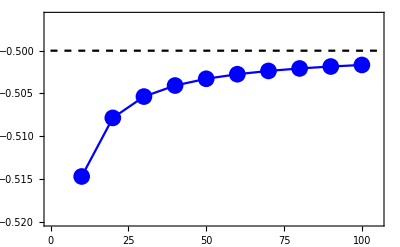

```mathematica
figdE=Show[ListPlot[{datdE1,datdE1},PlotRange->{{0,105},{-0.496,-0.52}},Joined->{True,False},Frame->True,LabelStyle->{Black,20},PlotStyle->{Blue,{Blue,PointSize[0.03]}}],Plot[Ec1,{x,0,105},PlotStyle->{Black,Dashed}]]
```

## Figure 2

```mathematica
H[x_,p_,g_,λ_]=(p^2+x^2)/2-(1/2)*(1+(2^(1/2)*g*x+λ)^2)^(1/2);
```

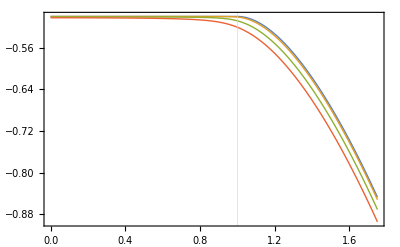

```mathematica
(*ground state energy as a function of g*)
GSQRM={};
GSAQRM1={};
GSAQRM2={};
GSAQRM3={};
ep=0.01;
Do[min=FindMinimum[H[x,0,gv,0],{x,-7,7}];
min1=FindMinimum[H[x,0,gv,0.01],{x,0,10}];
min2=FindMinimum[H[x,0,gv,0.05],{x,0,10}];
min3=FindMinimum[H[x,0,gv,0.1],{x,0,10}];
AppendTo[GSQRM,{gv,min[[1]]}];AppendTo[GSAQRM1,{gv,min1[[1]]}];
AppendTo[GSAQRM2,{gv,min2[[1]]}];
AppendTo[GSAQRM3,{gv,min3[[1]]}],{gv,0,1.75,ep}];

Evsg=ListPlot[{GSQRM,GSAQRM1,GSAQRM2,GSAQRM3},GridLines->{{1},{}},PlotStyle->Thick,GridLinesStyle->{{Thick,Black,Dashed},{}},Joined->True,Frame->True,LabelStyle->{Black,18}]
```

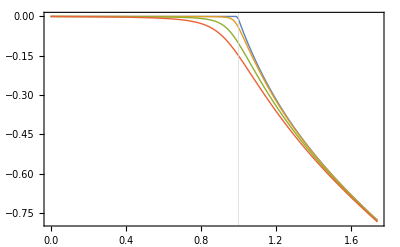

```mathematica
(*Derivative of the ground states energy as a function of g*)
DGSQRM={};
DGSAQRM1={};
DGSAQRM2={};
DGSAQRM3={};
Do[der=(GSQRM[[i+1,2]]-GSQRM[[i,2]])/ep;
der1=(GSAQRM1[[i+1,2]]-GSAQRM1[[i,2]])/ep;
der2=(GSAQRM2[[i+1,2]]-GSAQRM2[[i,2]])/ep;
der3=(GSAQRM3[[i+1,2]]-GSAQRM3[[i,2]])/ep;
AppendTo[DGSQRM,{GSQRM[[i,1]],der}];
AppendTo[DGSAQRM1,{GSAQRM1[[i,1]],der1}];
AppendTo[DGSAQRM2,{GSAQRM2[[i,1]],der2}];
AppendTo[DGSAQRM3,{GSAQRM3[[i,1]],der3}],{i,1,Length[GSQRM]-1}]

dEvsg=ListPlot[{DGSQRM,DGSAQRM1,DGSAQRM2,DGSAQRM3},Joined->True,PlotStyle->Thick,Frame->True,GridLines->{{1},{}},GridLinesStyle->{{Thick,Black,Dashed},{}},LabelStyle->{Black,18}]
```

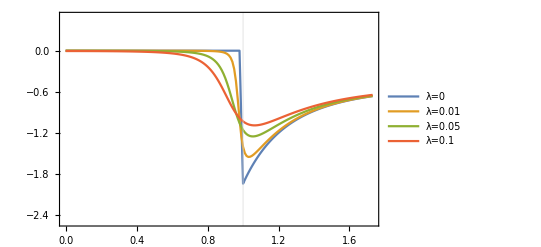

```mathematica
(*Second derivative of the ground states energy as a function of g*)D2GSQRM={};
D2GSAQRM1={};
D2GSAQRM2={};
D2GSAQRM3={};
Do[der=(DGSQRM[[i+1,2]]-DGSQRM[[i,2]])/ep;
der1=(DGSAQRM1[[i+1,2]]-DGSAQRM1[[i,2]])/ep;
der2=(DGSAQRM2[[i+1,2]]-DGSAQRM2[[i,2]])/ep;
der3=(DGSAQRM3[[i+1,2]]-DGSAQRM3[[i,2]])/ep;
AppendTo[D2GSQRM,{GSQRM[[i,1]],der}];
AppendTo[D2GSAQRM1,{GSAQRM1[[i,1]],der1}];
AppendTo[D2GSAQRM2,{GSAQRM2[[i,1]],der2}];
AppendTo[D2GSAQRM3,{GSAQRM3[[i,1]],der3}],{i,1,Length[DGSQRM]-1}]

d2Evsg=ListPlot[{D2GSQRM,D2GSAQRM1,D2GSAQRM2,D2GSAQRM3},PlotStyle->Thick,Joined->True,PlotRange->{All,{-2.5,0.5}},Frame->True,GridLines->{{1},{}},PlotLegends->{"λ=0","λ=0.01","λ=0.05","λ=0.1"},GridLinesStyle->{{Thick,Black,Dashed},{}},LabelStyle->{Black,18}]
```

## Figure 3

#### Wigner Function

```mathematica
datawigner=Import["/home/daniel/Documents/Codigos/RabiModel/src/output/wigner_eig_data.dat"];
datwignorm={};
Do[AppendTo[datwignorm,datawigner[[i]]];
If[datwignorm[[i,3]]<0,datwignorm[[i,3]]=2*datwignorm[[i,3]]],{i,1,Length[datawigner]}]
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

```mathematica
fac=0.5/0.35;
wigner2=Show[ListDensityPlot[datwignorm,PlotRange->{{-2.5,2.5},{-2.5,2.5},All},Frame->True,LabelStyle->{Black,22},ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)]]
```

-Graphics-

#### Discrete Wigner function

```mathematica
M={{0.00035825398413994114,0.4989824160306819},{0.49964174601586037,0.0010175839693183969}};
```

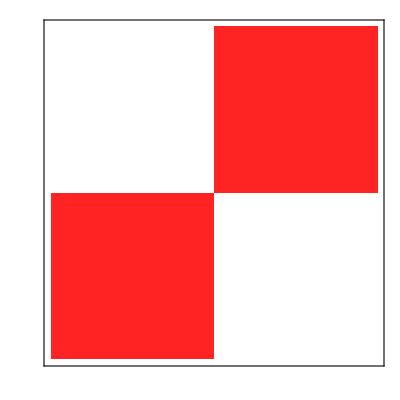

```mathematica
myColor[z_]:=Blend[{{-0.4,Blue},{0,White},{0.58,Red}},z]

figmat=MatrixPlot[M,ColorFunction->myColor,FrameTicks->None,ColorFunctionScaling->False,LabelStyle->{Black,12}(*,PlotLegends->Automatic*)]
```

## Figure 4

### Data

```mathematica
(*λ=0*)
DatMagR50λ0={{0,1.0003974759840055},{0.1,1.0003012350397769},{0.2,1.0000068830453341},{0.3,0.9999996059602758},{0.4,0.9999999630370194},{0.5,0.9999999956761295},{0.6,1.0000000205696007},{0.7,1.0000000057927467},{0.8,1.0000000015229544},{0.9,1.0000000140230967},{1,0.9999999973751855},{1.1,0.9999999982869967},{1.2,1.0000000005744936},{1.3,0.9999999999513918},{1.4,0.9999999851975832},{1.5,0.9999999986034815},{1.6,1.000000001461711},{1.7,1.000000000545184},{1.8,0.9999999996640765},{1.9,1.0000000000620937},{2,1.0000000001268858}};
DatManR50λ0={{0,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1,0},{1.1,0},{1.2,0},{1.3,0},{1.3,0},{1.4,0},{1.5,0},{1.6,0},{1.7,0},{1.8,0},{1.9,0},{2,0}};
DatNegR50λ0={{0,0},{0.05,0},{0.1,0},{0.15,0},{0.2,0},{0.25,0},{0.3,0},{0.35,0},{0.4,0},{0.45,0},{0.5,0},{0.55,0},{0.6,0},{0.65,0},{0.7,0},{0.75,0},{0.8,0},{0.85,0},{0.9,1*10^(-6)},{0.95,9.6*10^(-5)},{1,0.0028721938315612316},{1.025,0.012356555259824376},{1.05,0.045046985365931436},{1.075,0.1307916991903315},{1.1,0.2733874102764575},{1.125,0.38936523329485073},{1.15,0.4362242778645884},{1.175,0.4460885111407016},{1.2,0.44040837488184037},{1.25,0.41433117514498274},{1.3,0.38455247706474105},{1.35,0.35639368013159256},{1.4,0.33087341966824346},{1.45,0.30794844862649895},{1.5,0.28734309709107686},{1.55,0.2687654993931692},{1.6,0.25195532747756655},{1.65,0.23669221450165723},{1.7,0.22278777508091752},{1.75,0.21007710233871846},{1.8,0.19843810833889042},{1.85,0.1869269263497304},{1.9,0.17789491169926075},{1.95,0.16879059428329657},{2,0.1603653371543292}};
(*λ=10^-3*)
DatMagR50λ1={{0,1.001204887246488},{0.1,1.001094439454218},{0.2,1.0007780287261998},{0.3,1.0002236896204673},{0.4,0.9999998279369403},{0.5,0.9999995064493022},{0.6,0.9999999991432225},{0.7,1.000000000738561},{0.8,1.0000000004729397},{0.9,1.0000000013569967},{1.0,0.9999999992913188},{1.02,0.9999999899558624},{1.04,1.0000000197702479},{1.06,0.9999999955767767},{1.08,1.0153817742331266},{1.1,1.1242005527697745},{1.12,1.2955644134492543},{1.14,1.3761321203715426},{1.16,1.3964313864915694},{1.18,1.4033409130908097},{1.2,1.4062589069737077},{1.3,1.3965116764003436},{1.4,1.3707146319783363},{1.5,1.3413148663360766},{1.6,1.3123239067163104},{1.7,1.28561812540793},{1.8,1.2613137946772106},{1.9,1.2387424803448175},{2,1.219048905554533}};
DatManR50λ1={{0,0.000499749750187739},{0.1,0.00045635696520074376},{0.2,0.00032391932357844766},{0.3,9.519574090877114*10^-5},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,5.980598971477846*10^-5},{1,0},{1.02,0},{1.04,0},{1.06,0},{1.08,0.007656352581800752},{1.1,0.06206457576262514},{1.12,0.1477513509721975},{1.14,0.1880654417272718},{1.16,0.19820298098920408},{1.18,0.20166941332283117},{1.2,0.20312516197965702},{1.3,0.1982433161363022},{1.4,0.18534269320499008},{1.5,0.17061507117571617},{1.6,0.15613686897036017},{1.7,0.1426532669836399},{1.8,0.13698926108730558},{1.9,0.11936459705144942},{2,0.10949634074304404}};
DatNegR50λ1={{0,0.0019499552421993194},{0.1,0.002018256871650692},{0.2,0.002239175977357677},{0.3,0.002668326047969183},{0.4,0.00342969047158052316},{0.5,1.3344193068157223*10^-21},{0.6,2.373016636274041*10^-20},{0.7,3.6801945241693446*10^-5},{0.8,6.612162298324054*10^-12},{0.9,3.9687228961556253*10^-7},{1,0.004555208084351392},{1.02,0.009091726093875208},{1.04,0.027565470975232875},{1.06,0.07075742342533342},{1.08,0.14812793158334792},{1.1,0.2208739930027599},{1.12,0.1703571292452417},{1.14,0.06774386218639461},{1.16,0.018603213326505275},{1.18,0.005635322850625624},{1.2,0.0019843724533503693},{1.3,8.011286222342484*10^-5},{1.4,0.00012204271508975406},{1.5,0.000655175501885763},{1.6,0.003989568167285462},{1.7,0.0022388840664137044},{1.8,6.246303944523746*10^-6},{1.9,0.0003946326661927735},{2,1.9992265860580005*10^-5}};
(*λ=10^-2*)
DatMagR50λ2={{0,1.0100543846394},{0.1,1.0100456106149718},{0.2,1.0099923183617294},{0.3,1.0100497018966756},{0.4,1.0101991360214204},{0.5,1.0103694312062146},{0.6,1.0114006348160978},{0.7,1.012310691564124},{0.8,1.015682272466783},{0.9,1.025809388990558},{0.92,1.0302719464465055},{0.94,1.0361247474304083},{0.96,1.0447875087151994},{0.98,1.0581050607362912},{1,1.0779955154691465},{1.02,1.111061710316181},{1.04,1.1637929889390874},{1.06,1.2365208151650238},{1.08,1.3068567790400594},{1.12,1.3773741197815341},{1.14,1.3917428800437406},{1.16,1.4000663843126322},{1.18,1.404715154386985},{1.2,1.4067548309840836},{1.4,1.3696404248192593},{1.5,1.3403215016402241},{1.6,1.3114352459974565},{1.7,1.2848964452427676},{1.8,1.260173107764144},{1.9,1.2382205301141804},{2,1.2186192750887805}};
DatManR50λ2={{0,0.0049747518935922},{0.1,0.004974976064044068},{0.2,0.004978562142185727},{0.3,0.004995380288588258},{0.4,0.005046410799459888},{0.5,0.005174093873469676},{0.6,0.0054687266721134},{0.7,0.0061450336703189334},{0.8,0.007817066302199915},{0.9,0.01289757424322846},{1,0.03899606208394657},{1.02,0.05547807417349793},{1.04,0.08187730942307647},{1.06,0.11824664344041369},{1.08,0.15336885889388752},{1.1,0.17615008211627536},{1.12,0.18868282336644593},{1.14,0.19582496919241477},{1.16,0.20002613773684297},{1.18,0.20235610261780956},{1.2,0.20337221613741419},{1.3,0.19778711901028823},{1.4,0.18480241664887243},{1.5,0.17011638788490835},{1.6,0.1557054384003249},{1.7,0.14228809023056854},{1.8,0.1300846816830088},{1.9,0.11910663834998092},{2,0.10927905362504253}};
DatNegR50λ2={{0,3.47007192986748*10^-5},{0.1,3.910882456348297*10^-5},{0.2,5.38035039949758*10^-5},{0.3,8.416468845973135*10^-5},{0.4,0.0001528822021930054},{0.5,0.00023577771614946563},{0.6,0.0003856489642979355},{0.7,0.0011691752482236861},{0.8,0.00383704800086182},{0.9,0.001627446048003378},{1.4,0},{1.5,8.005567580304795*10^-5},{1.6,0.00012973699856222431},{1.7,0.0001272957090527882},{1.8,6.822772926295961*10^-6},{1.9,0.00038850730746275985},{2,1.9950171775917624*10^-5}};
```

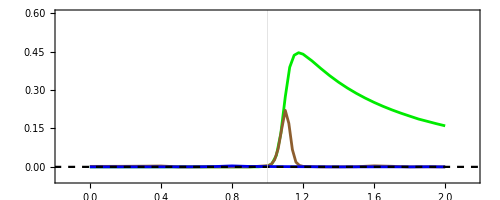

```mathematica
fig3a=Show[ListPlot[{DatNegR50λ0,DatNegR50λ1,DatNegR50λ2},Joined->True,Frame->True,Axes->False,PlotRange->{{-0.15,2.15},{-0.05,0.6}},PlotStyle->{{Darker[Green,0.08],Thickness[0.005]},{Darker[Brown,0.08],Thickness[0.005]},{Darker[Blue,0.08],Thickness[0.005]}},LabelStyle->{Black,15},GridLines->{{1},{}},GridLinesStyle->{Red,{}}],Plot[0.0,{x,-0.2,2.2},PlotStyle->{Black,Dashed}],AspectRatio->{0.05}]
```

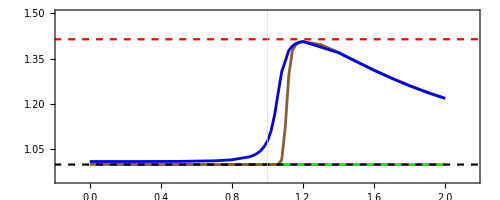

```mathematica
fig3c=Show[ListPlot[{DatMagR50λ0,DatMagR50λ1,DatMagR50λ2},Joined->True,Axes->False,Frame->True,PlotRange->{{-0.15,2.15},{0.95,1.5}},PlotStyle->{{Darker[Green,0.08],Thickness[0.005]},{Darker[Brown,0.08],Thickness[0.005]},{Darker[Blue,0.08],Thickness[0.005]}},LabelStyle->{Black,15},GridLines->{{1},{}},GridLinesStyle->{Red,{}}],Plot[1.0,{x,-0.2,2.2},PlotStyle->{Black,Dashed}],Plot[2^(1/2),{x,-0.2,2.2},PlotStyle->{Red,Dashed}],AspectRatio->{0.05}]
```

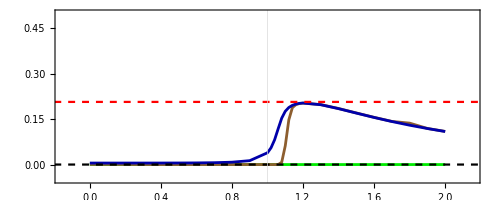

```mathematica
fig3b=Show[ListPlot[{DatManR50λ0,DatManR50λ1,DatManR50λ2},Joined->True,Frame->True,Axes->False,PlotRange->{{-0.15,2.15},{-0.05,0.5}},PlotStyle->{{Darker[Green,0.08],Thickness
[0.005]},{Darker[Brown,0.08],Thickness[0.005]},{Darker[Blue],Thickness[0.005]}},LabelStyle->{Black,15},GridLines->{{1},{}},GridLinesStyle->{Red,{}}],Plot[0.0,{x,-0.2,22},PlotStyle->{Black,Dashed}],Plot[(2^(1/2)-1)/2,{x,-0.2,2.2},PlotStyle->{Red,Dashed}],AspectRatio->{0.05}]
```

## Figure 5

### Data

```mathematica
(*Fixed g=1.2*)
(*R=10*)
DatMagR10={{0,0.9999999997492162},{0.005,1.0000000004011806},{0.008,0.9999999995032874},{0.01,1.004864681813356},{0.012,1.0389174409122777},{0.014,1.0701666635096685},{0.016,1.0987465348968115},{0.018,1.1246883397281422},{0.02,1.1480330082210046},{0.022,1.1691368352647655},{0.024,1.1880562499467227},{0.026,1.2051052527562638},{0.028,1.220343712174735},{0.03,1.233984419979471},{0.032,1.246272086361429},{0.034,1.2573077864065136},{0.036,1.2675071373647524},{0.038,1.2764760870740528},{0.04,1.2846447246725836},{0.042,1.2917861243267588},{0.044,1.2984892050796415},{0.046,1.3045648004614638},{0.048,1.3099331045331337},{0.05,1.3150376159761117}};
DatManR10={{0,0},{0.005,0},{0.01,0.0024322531785596624},{0.012,0.019437198228355546},{0.014,0.03507651916246646},{0.016,0.04935362365480778},{0.018,0.06231018264532051},{0.02,0.07401518080145864},{0.022,0.08455496019229258},{0.024,0.09402496537381166},{0.026,0.10252340674103566},{0.028,0.11014673729614133},{0.03,0.11698667031265653},{0.032,0.1231284096683376},{0.034,0.12864977685613077},{0.036,0.13362096424845227},{0.038,0.13810470031367794},{0.04,0.1421566664106122},{0.042,0.14505641548282455},{0.044,0.14915616110080276},{0.046,0.15218504611766226},{0.048,0.15494609257516068},{0.05,0.15746858209541914}};
DatNegR10={{0,0.058419691774695304},{0.005,0.057068459082349365},{0.008,0.05479971946932238},{0.01,0.05275921759054025},{0.012,0.050500465928650096},{0.014,0.04793318818878145},{0.016,0.04529671935814594},{0.018,0.04553883137704462},{0.02,0.03984463437437569},{0.022,0.037248726691664125},{0.024,0.034759379829696346},{0.026,0.03230007807520252},{0.028,0.029758048002906934},{0.03,0.027382746832881555},{0.032,0.025735899204726964},{0.034,0.02400984652650684},{0.036,0.02192728974109248},{0.038,0.020184015798248023},{0.04,0.018585227151825867},{0.042,0.017180505472940144},{0.044,0.015981408541195563},{0.046,0.01470941926687619},{0.048,0.013517332162993778},{0.05,0.012150895959484487}};
(*Fixed g=1.2*)
(*R=20*)
DatMagR20={{0,1.0000000005072052},{0.0005,0.9999999982036447},{0.001,0.9999999996910738},{0.0015,1.0424131518997504},{0.0018,1.0850202885240565},{0.002,1.1103924113790693},{0.003,1.2063000949526792},{0.004,1.2644276245148853},{0.005,1.3000657683059116},{0.006,1.3228073762892398},{0.007,1.3380518310139293},{0.008,1.3486316563388026},{0.009,1.356343148455851},{0.01,1.36211508497458},{0.011,1.366713425502002},{0.012,1.3699975194166158},{0.015,1.377000378555702},{0.02,1.3833031906622364},{0.03,1.38922318354789},{0.04,1.3922845867959568},{0.05,1.3945399884850997}};
DatManR20={{0,0},{0.001,0},{0.002,0.05518439048557178},{0.003,0.10314363996754339},{0.004,0.13211528708808506},{0.005,0.14993490223136552},{0.006,0.16134451055719312},{0.007,0.16897823569455284},{0.008,0.174300815035763},{0.009,0.17815115292153494},{0.01,0.18102797612374544},{0.011,0.18323908451955973},{0.012,0.18498118780008577},{0.015,0.18849734719726952},{0.02,0.19163436955929503},{0.03,0.19459051117396864},{0.04,0.1961372865972837},{0.05,0.19712887198606133}};
DatNegR20={{0,0.25353456343835945},{0.0005,0.24915767570359337},{0.001,0.23787803855640588},{0.0015,0.22097746474128632},{0.0018,0.2100534144243431},{0.002,0.20234200785408185},{0.003,0.16520414754182267},{0.004,0.13249193122922232},{0.005,0.10704923358686291},{0.006,0.08759336662001593},{0.007,0.07192155590930471},{0.008,0.06096819923946706},{0.009,0.051747160328614594},{0.01,0.04386810357478588},{0.011,0.03786486985334858},{0.012,0.034926891576938957},{0.015,0.02263912950705338},{0.02,0.012524614380106547},{0.03,0.0051453855599472575},{0.04,0.0022380981512093445},{0.05,0.0010615165782557057}};
(*Fixed g=1.2*)
(*R=50*)
DatMagR50={{0,1.0000000005744936},{0.00005,1.403262022783299},{0.0001,1.4054681500584594},{0.0005,1.4062038967770276},{0.001,1.4062589069737077},{0.05,1.4070932707654427}};
DatManR50={{0,0},{0.00005,0.2016298034841868},{0.001,0.20312516197965702},{0.05,0.203540799881627}};
DatNegR50={{0,0.44090252142868014},{0.00005,0.03870293774218414},{0.0001,0.018857827752681855},{0.0001,0.20273123160272366},{0.0005,0.0033760473602990615},{0.001,0.006759165260572519},{0.05,0.00010928200927162735}};
```

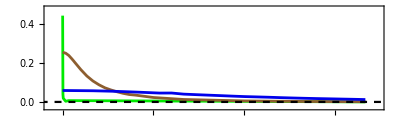

```mathematica
fig4a=Show[ListPlot[{DatNegR50,DatNegR20,DatNegR10},Joined->True,Frame->True,PlotRange->{{-0.002,0.052},{-0.03,0.48}},Axes->False,PlotStyle->{{Darker[Green,0.08],Thickness[0.005]},{Darker[Brown,0.08],Thickness[0.005]},{Darker[Blue,0.08],Thickness[0.005]}},LabelStyle->{Black,15},GridLines->{{1},{}},GridLinesStyle->{Red,{}}],Plot[0.0,{x,-0.2,2.2},PlotStyle->{Black,Dashed}],AspectRatio->0.3]
```

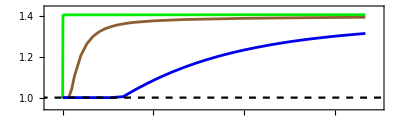

```mathematica
fig4c=Show[ListPlot[{DatMagR50,DatMagR20,DatMagR10},Joined->True,Frame->True,PlotRange->{{-0.002,0.052},{0.95,1.44}},PlotStyle->{{Darker[Green,0.08],Thickness[0.005]},{Darker[Brown,0.08],Thickness[0.005]},{Darker[Blue,0.08],Thickness[0.005]}},LabelStyle->{Black,15},GridLines->{{1},{}},GridLinesStyle->{Red,{}}],Plot[1.0,{x,-0.2,2.2},PlotStyle->{Black,Dashed}],AspectRatio->0.3]
```

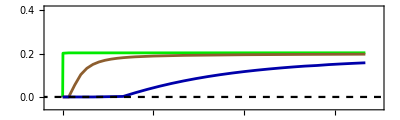

```mathematica
fig4b=Show[ListPlot[{DatManR50,DatManR20,DatManR10},Joined->True,Frame->True,PlotRange->{{-0.002,0.052},{-0.05,0.41}},Axes->False,PlotStyle->{{Darker[Green,0.08],Thickness
[0.005]},{Darker[Brown,0.08],Thickness[0.005]},{Darker[Blue],Thickness[0.005]}},LabelStyle->{Black,15},GridLines->{{1},{}},GridLinesStyle->{Red,{}}],Plot[0.0,{x,-0.2,22},PlotStyle->{Black,Dashed}],AspectRatio->0.3]
```

```mathematica
Export["Fig4b.png",fig4b]
```

Fig4b.png

## Figure 6

```mathematica
gt=1.2;
λt=0.0;
H[x_,p_,g_,λ_]=(p^2+x^2)/2-(1/2)*(1+(2^(1/2)*g*x+λ)^2)^(1/2);
FindMinimum[H[x,0,gt,λt],{x,-7,7}]
h0=-0.5336111110769508;
E0=-53.50474569124572/100;
Ecq=h0-(E0-h0);
```

{-0.533611,{x→0.610567}}

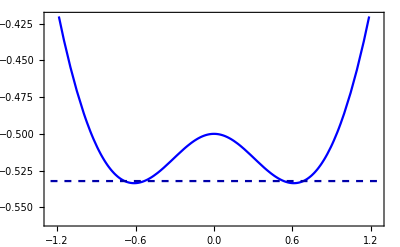

```mathematica
figpot=Show[Plot[H[x,0,gt,λt],{x,-1.25,1.25},PlotStyle->Blue,PlotRange->{{-1.25,1.25},{-0.56,-0.42}},Frame->True,LabelStyle->{Black,20},Axes->None],Plot[Ecq,{x,-1.25,1.25},PlotStyle->{Darker[Blue],Dashed}]]
```